# EIWL Sections 14, 17 - Harper Yonago

## Section 14

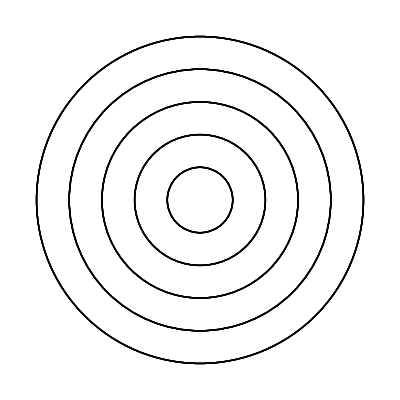

```mathematica
Graphics[Table[Circle[{0,0},r],5,{r,1,5,1}]]
```

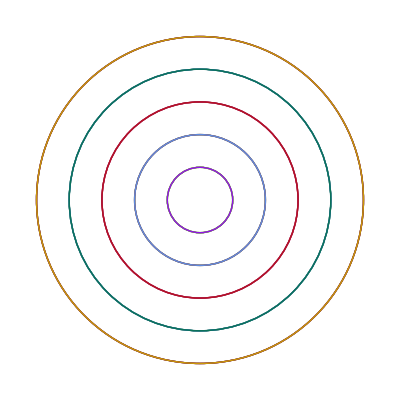

```mathematica
Graphics[Table[Style[Circle[{0,0},r],RandomColor[]],5,{r,1,5,1}]]
```

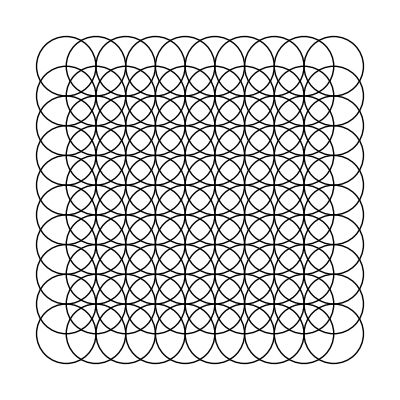

```mathematica
Graphics[Table[Circle[{x,y},1],{x,1,10,1},{y,1,10,1}]]
```

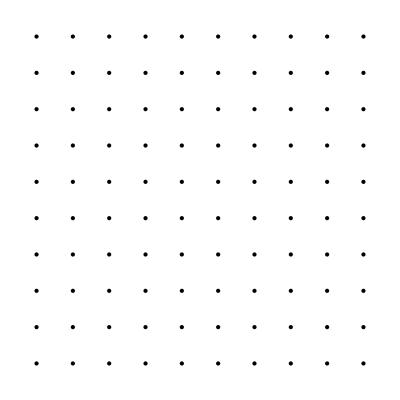

```mathematica
Graphics[Table[Point[{x,y}],{x,1,10,1},{y,1,10,1}]]
```

```mathematica
Manipulate[Graphics[Table[Circle[{0,0},x],{x,n}]],{n,1,20,1}]
```

```mathematica
Graphics3D[Table[Style[Sphere[{RandomInteger[10],RandomInteger[10],RandomInteger[10]}],RandomColor[]],50]]
```

-Graphics3D-

```mathematica
Graphics3D[Table[Style[Sphere[{x,y,z},0.5],RGBColor[r,g,b]],{x,1,11,1},{y,1,11,1},{z,1,11,1},{r,0,1,0.1},{g,0,1,0.1},{b,0,1,0.1}]]
```

```mathematica
(*I cannot figure out how to do this one*)
```

```mathematica
Manipulate[Graphics[Table[Circle[{t*x,0},x],{x,1,10}]],{t,-2,2}]
```

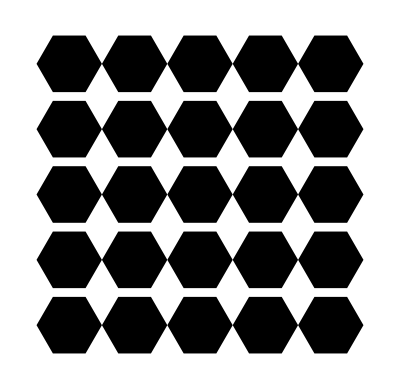

```mathematica
Graphics[Table[RegularPolygon[{x,y},0.5,6],{x,1,5},{y,1,5}]]
```

```mathematica
Graphics3D[Line[Table[RandomInteger[50],50,3]]]
```

-Graphics3D-

```mathematica
Manipulate[Graphics3D[Style[{Dodecahedron[{0,0,0},2],Icosahedron[{0,0,0},x]},Opacity[0.5]]],{x,1,2}]
```

## Section 17

```mathematica
UnitConvert[Quantity[4.5, "Pounds"],"Kilograms"]
```

2.04117 kg

```mathematica
UnitConvert[Quantity[60.25, ("Miles")/("Hours")],"km/h"]
```

96.963 km/h

```mathematica
UnitConvert[Entity["Building","EiffelTower::5h9w8"][EntityProperty["Building","Height"]],"Miles"]
```

0.205052 mi

```mathematica
/
```

26.8147

```mathematica
/
```

81.3

```mathematica
CurrencyConvert[,"USDollars"]
```

16.14 $

```mathematica
UnitConvert[Quantity[35, "Ounces"] + Quantity[0.25, "ShortTons"] + Quantity[45, "Pounds"] + Quantity[9, "Stones"],"Kilograms"]
```

305.353 kg

```mathematica
UnitConvert[["DistanceFromEarth"],"LightMinutes"]
```

{11.7362 light minutes,4.21871 light minutes,0. light minutes,5.76486 light minutes,38.0364 light minutes,86.7466 light minutes,161.128 light minutes,254.497 light minutes}

```mathematica
Rotate["hello",180Degree]
```

hello

```mathematica
Table[Rotate[Style["A",100],d],{d,0,360,30}]
```

{A,A,A,A,A,A,A,A,A,A,A,A,A}

```mathematica
Manipulate[Rotate[-Graphics-,d],{d,0,180}]
```

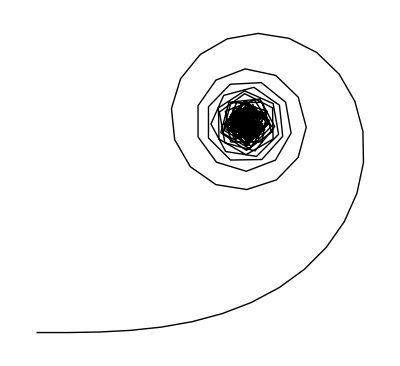

```mathematica
Graphics[Line[AnglePath[Table[n Degree,{n,0,180}]]]]
```

```mathematica
Manipulate[Graphics[Line[AnglePath[Table[Degree n, 100]]]],{n,1,100}]
```

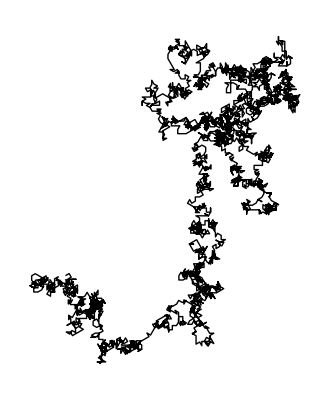

```mathematica
Graphics[Line[AnglePath[30 Degree IntegerDigits[2^10000]]]]
```

## Some Research and a Graph

```mathematica
["Image"]
```

Missing[UnknownProperty,{City,Image}]

```mathematica
Table[Part[,x]["PopulationDensity"],{x,53}]
```

{4409. people/mi^2,3113. people/mi^2,8444. people/mi^2,5992. people/mi^2,2494. people/mi^2,3024. people/mi^2,9093. people/mi^2,7914. people/mi^2,Missing[NotApplicable],Missing[NotApplicable],18698. people/mi^2,1351. people/mi^2,3673. people/mi^2,9735. people/mi^2,7751. people/mi^2,9358. people/mi^2,7704. people/mi^2,6951. people/mi^2,2367. people/mi^2,2189. people/mi^2,3535. people/mi^2,3881. people/mi^2,2908. people/mi^2,4068. people/mi^2,4513. people/mi^2,4007. people/mi^2,Missing[NotApplicable],3745. people/mi^2,2137. people/mi^2,57. people/mi^2,8104. people/mi^2,8930. people/mi^2,5194. people/mi^2,Missing[NotApplicable],4880. people/mi^2,Missing[NotApplicable],Missing[NotApplicable],Missing[NotApplicable],Missing[NotApplicable],Missing[NotAvailable],Missing[NotApplicable],Missing[NotApplicable],Missing[NotApplicable],5938. people/mi^2,Missing[NotApplicable],Missing[NotApplicable],Missing[NotApplicable],Missing[NotApplicable],Missing[NotApplicable],Missing[NotApplicable],Missing[NotApplicable],Missing[NotApplicable],Missing[NotApplicable]}

```mathematica
Table[Part[,x]["AverageHouseValue"],{x,35}]
```

{596 400.00 $,543 700.00 $,602 400.00 $,597 400.00 $,392 300.00 $,Missing[NotApplicable],554 500.00 $,400 800.00 $,Missing[NotApplicable],Missing[NotApplicable],555 000.00 $,801 300.00 $,530 100.00 $,695 300.00 $,501 000.00 $,642 200.00 $,575 300.00 $,351 000.00 $,464 100.00 $,406 300.00 $,556 500.00 $,362 700.00 $,657 000.00 $,375 900.00 $,459 400.00 $,540 900.00 $,Missing[NotApplicable],600 700.00 $,350 800.00 $,725 100.00 $,660 000.00 $,299 500.00 $,334 800.00 $,Missing[NotApplicable],628 100.00 $}

```mathematica
Table[Part[,x]["PersonsPerHousehold"],{x,35}]
```

{2.32 people,2.78 people,1.68 people,2.16 people,2.47 people,1.36 people,1.44 people,2.4 people,Missing[NotApplicable],Missing[NotApplicable],1.45 people,1.72 people,2.35 people,2.35 people,2.24 people,1.88 people,2.25 people,2.46 people,2.18 people,2.48 people,2.41 people,2.46 people,2.43 people,2.32 people,2.5 people,1.86 people,Missing[NotApplicable],2.73 people,2.61 people,2.38 people,1.73 people,2.87 people,2.97 people,Missing[NotApplicable],1.92 people}

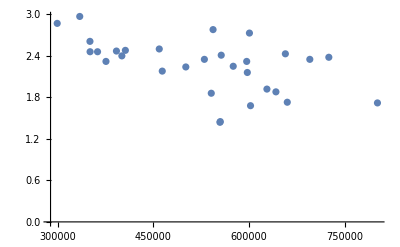

```mathematica
ListPlot[Transpose[{Table[Part[,x]["AverageHouseValue"],{x,35}],Table[Part[,x]["PersonsPerHousehold"],{x,35}]}]]
```